# NSTX ECH with linear Slab Profiles

## Open Additional files:

## Get dispersion routines by evaluating Disper.nb Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (Fast and Slow roots) n_z = 0.1

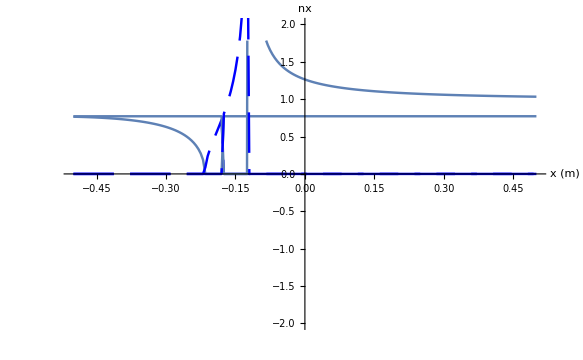

dataSet=Slab 90HHz

xProfileMin=-0.5

xProfileMax=0.5

nXmin=4.×10^19

nXmax=4.×10^19

BXmin=0.2151

BXmax=6.2151

freq=90000

nz=0.1

etaList={0.,1.,0.,0.,0.}

xmin=-0.5

xmin=-0.5

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=myComplexListPlot[nF,"x (m)","nx"];
g2=myComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (Fast and Slow roots) n_z = 0.3

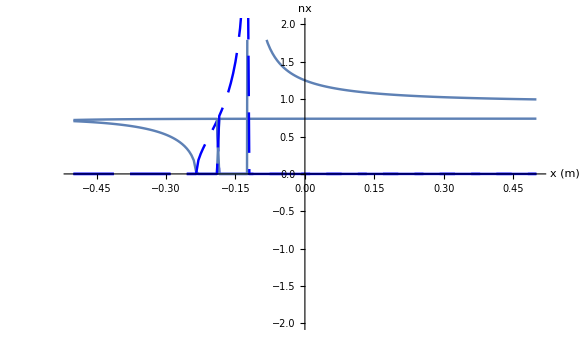

dataSet=Slab 90HHz

xProfileMin=-0.5

xProfileMax=0.5

nXmin=4.×10^19

nXmax=4.×10^19

BXmin=0.2151

BXmax=6.2151

freq=90000

nz=0.3

etaList={0.,1.,0.,0.,0.}

xmin=-0.5

xmin=-0.5

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=myComplexListPlot[nF,"x (m)","nx"];
g2=myComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

```mathematica
■^*
```

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (Fast and Slow roots) n_z = 0.6

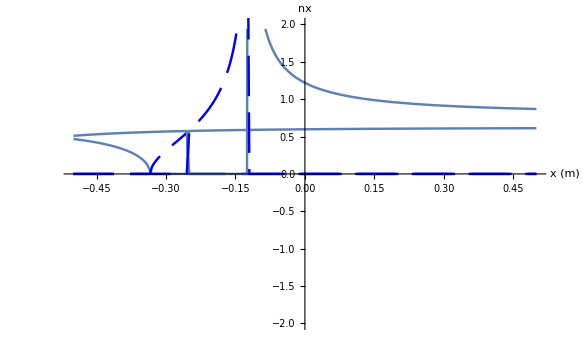

dataSet=Slab 90HHz

xProfileMin=-0.5

xProfileMax=0.5

nXmin=4.×10^19

nXmax=4.×10^19

BXmin=0.2151

BXmax=6.2151

freq=90000

nz=0.6

etaList={0.,1.,0.,0.,0.}

xmin=-0.5

xmin=-0.5

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=myComplexListPlot[nF,"x (m)","nx"];
g2=myComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (Fast and Slow roots) n_z = 0.65

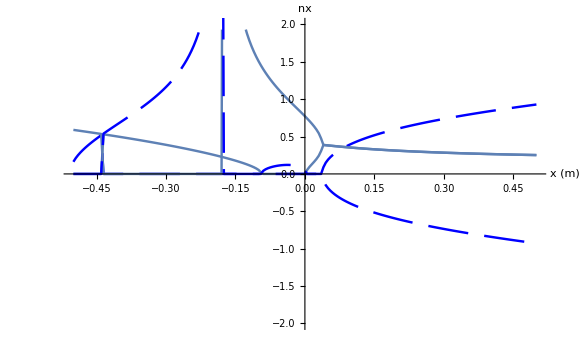

dataSet=Slab 90HHz

xProfileMin=-0.5

xProfileMax=0.5

nXmin=3.×10^19

nXmax=1.7×10^20

BXmin=1.60755

BXmax=1.60755

freq=90000

nz=0.65

etaList={0.,1.,0.,0.,0.}

xmin=-0.5

xmin=-0.5

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=myComplexListPlot[nF,"x (m)","nx"];
g2=myComplexListPlot[nS,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (Plus and Minus roots)

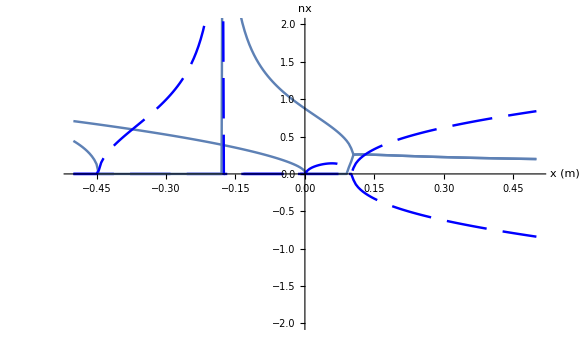

dataSet=Slab 90HHz

xProfileMin=-0.5

xProfileMax=0.5

nXmin=3.×10^19

nXmax=1.7×10^20

BXmin=1.60755

BXmax=1.60755

freq=90000

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=-0.5

xmin=-0.5

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2PM[freq,ne,b,nz,etaList]]
nt2PM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦2⟧}];
nM=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦3⟧}];
g1=myComplexListPlot[nP,"x (m)","nx"];
g2=myComplexListPlot[nM,"x (m)","nx"];
Show[{g1,g2},PlotRange->{-2.,2.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

```mathematica
nPerp2FS[x_]
```

dataSet=DIII-D slab

xProfileMin=-0.68

xProfileMax=0.68

nXmin=2.5×10^19

nXmax=3.5×10^19

BXmin=1.9

BXmax=2.1

freq=55990

nz=0.1

etaList={1.,0.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=-0.68

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

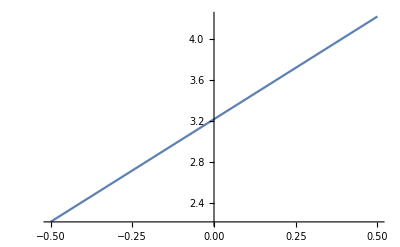

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

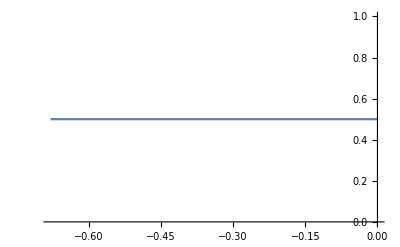

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

```mathematica
αHcut[1.60755,90*10^3, 0.2,1.]
αHcut[1.60755,90*10^3, 0.2,-1.]
```

1.43999

0.480005

## Initialization

#### Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```

```mathematica
tprof[x_]:=If[Abs[(TXmax-TXmin)/TXmax]>10^-6,TXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TXmax-TXmin),TXmin];
```

```mathematica
αHcut[B_,freq_, nz_,s_]:=(1.-nz^2)(1.+s*2.79926*10^4 B/freq)
```